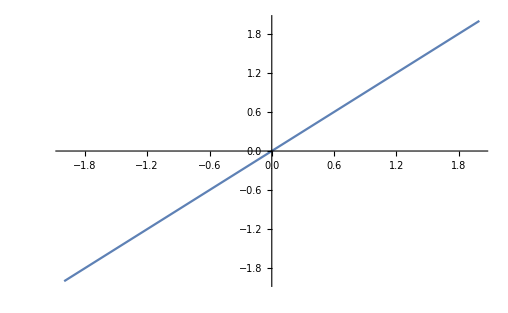

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
Series[Log[x],{x,0,10}]
```

Log[x]+O[x]^11

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
FullSimplify[Normalize@{x,x-x^3/6+x^5/120-x^7/5040+x^9/362880}.Normalize@{x,Sin[x]},x∈Reals]
```

(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))

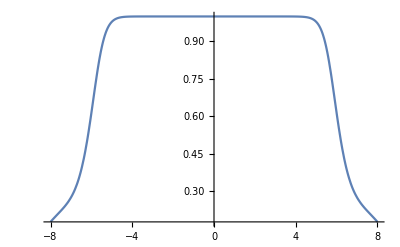

```mathematica
Plot[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2))),{x,-8,8}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,x-x^3/6+x^5/120-x^7/5040+x^9/362880}.Normalize@{x,Sin[x]}],x∈Reals]
```

Abs[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(√((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))]/362880

```mathematica
Plot[Abs[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(√((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))]/362880,{x,-8,8}]
```

-Graphics-

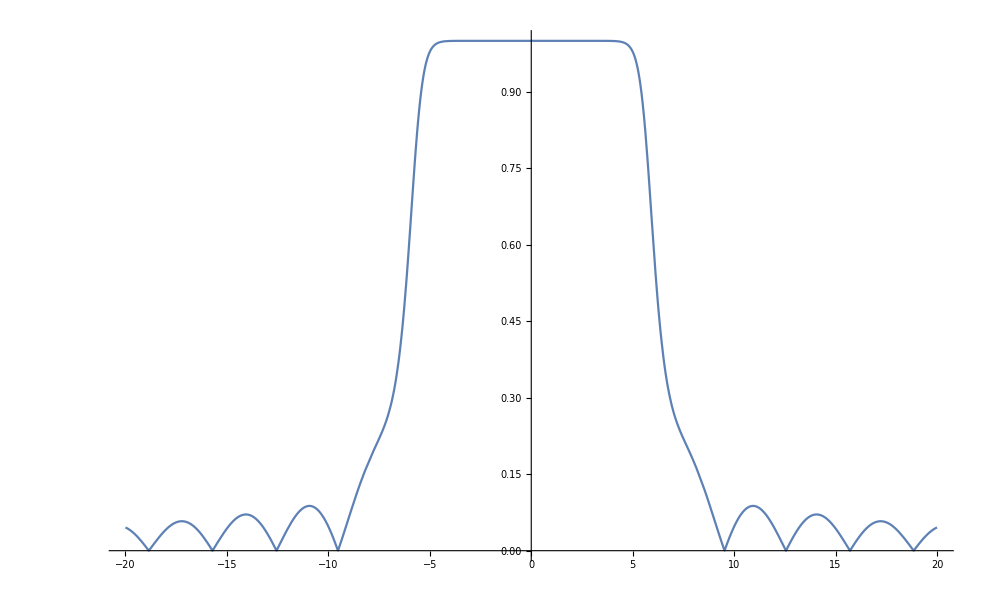

```mathematica
Plot[Abs[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(√((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))]/362880,{x,-20,20},PlotRange->Full]
```

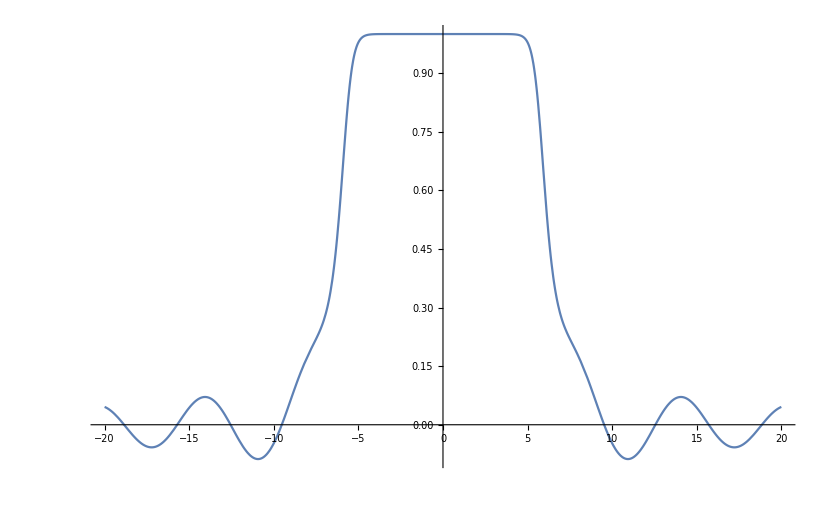

```mathematica
Plot[((x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(√((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2))))/362880,{x,-20,20},PlotRange->Full]
```

```mathematica
FullSimplify[((x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(√((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2))))/362880==Normalize@{x,x}.Normalize@{x,f[x]},{x,f[x]}∈Reals]
```

(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))==((x+f[x]) Sign[x])/(√2 √(x^2+f[x]^2))

```mathematica
Solve[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))==((x+f[x]) Sign[x])/(√2 √(x^2+f[x]^2)),f[x],Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))==((x+f[x]) Sign[x])/(√2 √(x^2+f[x]^2)),f[x],ℝ]

```mathematica
Piecewise[{{x,x<0},{Log[x],x>0},0}]
```

Piecewise::pairs: The first argument {{x,x<0},{Log[x],x>0},0} of Piecewise is not a list of pairs.

Piecewise[{{x,x<0},{Log[x],x>0},0}]

```mathematica
Piecewise[{{x,x<0},{Log[x],x>0}},0]
```

Piecewise[{{x, x<0}, {Log[x], x>0}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{x,x<0},{Log[x],x>0}},0]]
```

Piecewise[{{x, x<0}, {Log[x], x>0}, {0, True}}]

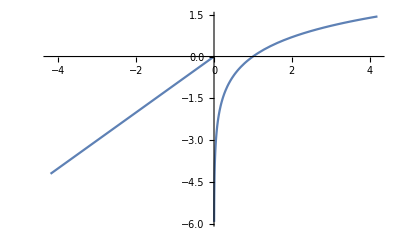

```mathematica
Plot[Piecewise[{{x,x<0},{Log[x],x>0}},0],{x,-4.2,4.2}]
```